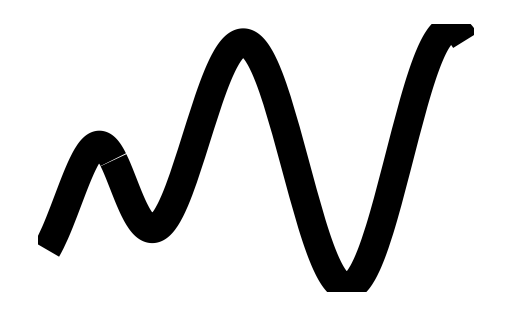

icon.png

icon.ico

```mathematica
ClearAll["Global`*"]

d =.0001;
th=.04;

sine=Plot[
Sin[x*2Pi],
{x,0,1+d},
PlotStyle->{Black,Thickness[th]},
Axes->False
];

triangle=Plot[
TriangleWave[x],
{x,0,1+d},
PlotStyle->{Black,Thickness[th]},
Axes->False
];

rampup=Plot[
SawtoothWave[x],
{x,0,1+d},
Exclusions->None,
PlotStyle->{Black,Thickness[th]},
Axes->False
];

rampdown=Plot[
SawtoothWave[-x],
{x,0-d,1},
Exclusions->None,
PlotStyle->{Black,Thickness[th]},
Axes->False
];

square= Plot[
Piecewise[{{0,x<0}, {1, x<.5},{-1,x<1-d}, {0,x>1-d}}],
{x,0-d,1},
Exclusions->None,
PlotStyle->{Black,Thickness[th]},
Axes->False
];

random=Plot[
Piecewise[{{0,x<0}, {.23, x<.25},{-.55,x<.5}, {1,x<.75},{.6,x<1-d},{0,x>1-d}}],
{x,0-d,1},
Exclusions->None,
PlotStyle->{Black,Thickness[th]},
Axes->False
];

smthrand=Plot[
Sin[x*2Pi+2]*3ArcTan[x*2Pi-2],
{x,0,2+d},
PlotStyle->{Black,Thickness[th]},
Axes->False
];

icon = Plot[
Sin[x*2Pi+2]*3ArcTan[x*2Pi-2],
{x,0,2+d},
PlotStyle->{Black,Thickness[th]},
Axes->False,
ImageSize-> {512,512}
];


(*Export["icon.png",icon]
Export["icon.ico",icon]*)

(*Export["sine.svg",sine]
Export["triangle.svg",triangle]
Export["rampup.svg",rampup]
Export["rampdown.svg",rampdown]
Export["square.svg",square]
Export["random.svg",random]
Export["smthrand.svg",smthrand]*)
```